Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# Práctica 3 (24 de septiembre de 2024) Números complejos

Se trataría de poder expresar un número complejo de diferentes formas (binómica, polar, exponencial y trigonométrica) y de saber calcular sumas, productos, inversos, cocientes, raíces, exponenciales, logaritmos, potencias, senos y cosenos.
La forma binómica consiste en poner la parte real y la parte imaginaria, z= a + i b.
Las otras formas necesitan del módulo y el argumento del número complejo.

Conocidos el módulo y el argumento podríamos escribir r_θ, siendo r el módulo y θ el argumento. Es la forma polar.
La forma trigonométrica sería escribirlo como r (cos θ + i sen θ) y la exponencial r e^(i θ).

Ciertas operaciones son más fáciles en forma binómica y otras en forma polar (o sus variantes).

Con el programa Mathematica podemos trabajar con números complejos. La unidad imaginaria se escribe I, letra i mayúscula, o usando la paleta, ⅈ.

Sumas, productos, inversos, cocientes, potencias, raíces, exponenciales, logaritmos, senos o cosenos, módulos y argumentos, se deberían poder calcular sin el Mathematica y después podríamos comprobar.

## Ejemplos

## Calcular Parte real de 3+2ⅈ Parte imaginaria de 3+2ⅈ (3+2ⅈ) + (4-3ⅈ) (3+2ⅈ)(4-3ⅈ) 1/(4-3ⅈ) Conjugado de 3+2ⅈ (3+2ⅈ)/(4-3ⅈ) Módulo de (2+3ⅈ) Argumento de (2+3ⅈ) (2+3ⅈ)^8 Raíz séptima de -1 Soluciones de la ecuación z^7+1=0 Exponencial de 3+2ⅈ Logaritmo de 3+2ⅈ Seno de 3+2ⅈ Coseno de 3+2ⅈ

Parte real de 3 + 2 ⅈ

```mathematica
Re[3+2ⅈ]
```

3

Parte imaginaria de 3 + 2 ⅈ

```mathematica
Im[3+2ⅈ]
```

2

Suma de dos números complejos (se suman las partes reales y se suman las partes imaginarias)

```mathematica
(3+2ⅈ)+ (4-3ⅈ)
```

7-ⅈ

Producto de dos números complejos (se multiplican todos los sumandos por todos los sumandos y se tiene en cuenta que ⅈ por ⅈ es -1)

```mathematica
(3+2ⅈ)* (4-3ⅈ)
```

18-ⅈ

Inverso de un número complejo (se puede multiplicar y dividir por el conjugado)

```mathematica
1/(4-3ⅈ)
```

4/25+(3 ⅈ)/25

Conjugado de un número complejo (se trata de cambiar de signo la parte imaginaria)

```mathematica
Conjugate[4-3ⅈ]
```

4+3 ⅈ

División de dos números complejos (igual que para el inverso, se puede multiplicar y dividir por el conjugado)

```mathematica
(3+2ⅈ)/ (4-3ⅈ)
```

6/25+(17 ⅈ)/25

Módulo de un número complejo (sería como el módulo de un vector, raíz cuadrada de la suma del cuadrado de la parte real y del cuadrado de la parte imaginaria) (con el Mathematica se usa la misma función que para calcular el valor absoluto).

```mathematica
Abs[2+3ⅈ]
```

√13

Calcular el argumento de un número complejo (cuidado con la función arcotangente!!!) En realidad, habría infinitos ángulos asociados a un número complejo y que difieren en múltiplos enteros de 2π (vueltas completas). En algunos libros se habla de Argumento principal para referirse a uno de ellos y que está en un intervalo de longitud 2π y que podría ser (-π,π].

```mathematica
Arg[2+3ⅈ]
```

ArcTan[3/2]

```mathematica
N[%]
```

0.982794

```mathematica
Arg[-2-3ⅈ]
```

-π+ArcTan[3/2]

```mathematica
N[%]
```

-2.1588

Dado que el número 2+3ⅈ está en el primer cuadrante (las dos partes, real e imaginaria, son positivas) el ángulo debería estar entre 0 y π/2 radianes. Hay ángulos entre π y 3π/2 con la misma tangente, pero no tendrían el mismo argumento.

Calcular potencias de un número complejo (2+3ⅈ)^8

```mathematica
(2+3I)^8
```

-239+28560 ⅈ

Para calcular las potencias de un número complejo “a mano” puede ser más conveniente escribir el número complejo en forma polar. De esta forma, la potencia octava sería calcular la potencia octava de su módulo (así obtendríamos el módulo del resultado) y multiplicaríamos el argumento por 8 (así obtendríamos el argumento del resultado).  

El módulo de (2+3ⅈ) es √13 y su argumento es ArcTan[3/2].

```mathematica
√13^8
```

28561

```mathematica
8 ArcTan[3/2]
```

8 ArcTan[3/2]

```mathematica
(2+3 I)^8==28561(Cos[8 ArcTan[3/2]]+I Sin[8 ArcTan[3/2]])
```

True

Calculo de la raíz séptima de -1.

```mathematica
ComplexExpand[-1^(1/7)]
```

Cos[π/7]+ⅈ Sin[π/7]

Calculo de la raíz con la ecuación polinómica y Solve.

```mathematica
ComplexExpand[Solve[z^7==-1,z]]
```

{{z→-1},{z→Cos[π/7]+ⅈ Sin[π/7]},{z→-ⅈ Cos[(3 π)/14]-Sin[(3 π)/14]},{z→ⅈ Cos[π/14]+Sin[π/14]},{z→-ⅈ Cos[π/14]+Sin[π/14]},{z→ⅈ Cos[(3 π)/14]-Sin[(3 π)/14]},{z→Cos[π/7]-ⅈ Sin[π/7]}}

Dibujo de las raíces (todas tienen el mismo módulo, que es la distancia al (0,0), y están en la misma circunferencia. En cuanto a los argumentos, se diferencian en múltiplos de 2π /7.

```mathematica
raices=Table[1(Cos[π/7+2π n/7]+ⅈ Sin[π/7+2π n/7]),{n,0,6}];
```

```mathematica
puntos=Table[{Re[raices[[n]]],Im[raices[[n]]]},{n,1,7}];
```

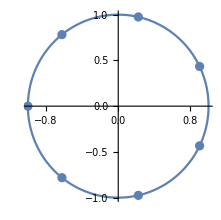

```mathematica
Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}], ListPlot[puntos,PlotStyle->PointSize[0.03]],AspectRatio->Automatic]
```

Calculo de la exponencial de un número complejo (es un número complejo cuyo módulo es la exponencial de la parte real y cuyo argumento es la parte imaginaria).

```mathematica
E^(3+2I)
```

ⅇ^(3+2 ⅈ)

```mathematica
ComplexExpand[E^(3+2I)]
```

ⅇ^3 Cos[2]+ⅈ ⅇ^3 Sin[2]

Cálculo del logaritmo de un número complejo (es un número complejo cuya parte real es el logaritmo del módulo y cuya parte imaginaria es el argumento) (como el argumento son infinitos valores, habría infinitos logaritmos).

```mathematica
Log[3+2I]
```

Log[3+2 ⅈ]

```mathematica
ComplexExpand[Log[3+2I]]
```

ⅈ ArcTan[2/3]+Log[13]/2

Todos los logaritmos tendrían la misma parte real y se diferenciarían en la parte imaginaria que se diferenciarían en múltiplos de 2π.

Cálculo del coseno de un número complejo (es la semisuma de la exponencial de ⅈ z y de - ⅈ z)
		cos(a + ⅈ b) = 1/2 (ⅇ^b (Cos[a]-ⅈ Sin[a])+ⅇ^-b(Cos[a]+ⅈ Sin[a]))

```mathematica
(E^(-3)(Cos[2]+I Sin[2])+E^3(Cos[-2]+I Sin[-2]))/2
```

1/2 (ⅇ^3 (Cos[2]-ⅈ Sin[2])+(Cos[2]+ⅈ Sin[2])/ⅇ^3)

```mathematica
Cos[2+3I]
```

Cos[2+3 ⅈ]

```mathematica
ComplexExpand[Cos[2+3I]]
```

Cos[2] Cosh[3]-ⅈ Sin[2] Sinh[3]

```mathematica
Cos[2+3I]==(E^(-3)(Cos[2]+I Sin[2])+E^3(Cos[-2]+I Sin[-2]))/2//Simplify
```

True

Cálculo del seno de un número complejo (es la diferencia de la exponencial de ⅈ z y de - ⅈ z, dividida entre 2 ⅈ)
	sen (a + ⅈ b) = 1/(2ⅈ) (ⅇ^-b (Cos[a]+ⅈ Sin[a])-ⅇ^b(Cos[a]-ⅈ Sin[a]))

```mathematica
Sin[2+3I]
```

Sin[2+3 ⅈ]

```mathematica
ComplexExpand[Sin[2+3I]]
```

Cosh[3] Sin[2]+ⅈ Cos[2] Sinh[3]

```mathematica
Sin[2+3I]==(E^(-3)(Cos[2]+I Sin[2])-E^3(Cos[-2]+I Sin[-2]))/(2I)//Simplify
```

True

## Completar la tabla (Forma binómica | a+ i b | i | 2 | □ | □ | □ | □ | □ Forma polar | r_θ | □ | □ | 3_π | 2_(-π/2) | □ | □ | □ Forma trigonométrica | r (cos θ+i sen θ) | □ | □ | □ | □ | 3 (cos π/2+i sen π/2) | 2 (cos π+i sen π) | □ Forma exponencial | r e^(i θ) | □ | □ | □ | □ | □ | □ | 3 e^(i π/3))

Solución

Forma binómica | ⅈ | 2 | -3 | -2 ⅈ | 3ⅈ | -2 | 1/2+ⅈ(√3)/2
Forma polar | 1_(π/2) | 2_0 | 3_π | 2_(-π/2) | 3_(π/2) | 2_π | 1_(π/3)
Forma trigonométrica | 1 (Cos π/2+ ⅈ Sen π/2) | 2 (Cos 0+ ⅈ Sen 0) | 3 (Cos π+ ⅈ Sen π) | 2 (Cos -π/2+ ⅈ Sen -π/2) | 3 (cos π/2+i sen π/2) | 2 (cos π+i sen π) | 1(cos π/3+ ⅈ sen π/3)
Forma exponencial | 1 e^(i π/2) | 2 e^(i 0) | 3 e^(i π) | 2 e^(i -π/2) | 3 e^(i π/2) | 2 e^(i π) | e^(i π/3)